# General Relativistic Vorticity Solver

## Input Parameters

## Metric

### Available metrics

```mathematica
ggschwarz = { {  1-rs/r,   0         ,      0       ,     0                         },
          {     0         , - 1/(1-rs/r),      0       ,     0                         },
          {     0         ,     0       ,      -r^2     ,     0                        },
          {     0         ,     0       ,      0       , -r^2 Sin[θ]^2  }};
ggminkowski={ {  1,   0         ,      0       ,     0                         },
          {     0         , -1,      0       ,     0                         },
          {     0         ,     0       ,      -1     ,     0                        },
          {     0         ,     0       ,      0       , -1  }};
ggFLRW={ {  1,   0         ,      0       ,     0                         },
          {     0         , - a[t]^2/(1-k r^2),      0       ,     0                         },
          {     0         ,     0       ,      -a[t]^2 r^2     ,     0                        },
          {     0         ,     0       ,      0       , -a[t]^2 r^2 Sin[θ]^2  }};
a[t_]=Exp[0.1 t];k=0;
ggKerr={ {  1-(rs r)/ρ2        ,   0      ,     0   , rs r α Sin[θ]^2     },
          {     0                       , - ρ2/Δ   ,    0   ,       0                         },
          {     0                       ,     0      , -ρ2  ,      0                          },
          { rs r α Sin[θ]^2,     0     , 0       , -(r^2+α^2+(rs r α^2)/ρ2 Sin[θ]^2)Sin[θ]^2  }};
rs=2m;α=J/m;ρ2=r^2+α^2 Cos[θ]^2;Δ=r^2-rs r+α^2;
```

### Choose input metric/coordinate

```mathematica
gg=ggKerr;
d = 4;
xx = {t,r,θ,ϕ};
```

#### Allocate arrays used later

```mathematica
xxVorsphe=xx /.t->t[τ]/.r->r[τ]/.θ->θ[τ]/.ϕ->ϕ[τ];
xxtsphe=xx /.r->r[τ]/.θ->θ[τ]/.ϕ->ϕ[τ];
xxVor=xxVorsphe;
xxt=xxtsphe;
```

## Physical Parameters

### Initial Conditions

Conserved canonical momentum associated with ϕ and t Lagrangian independence (constants of motion)
Initial radius, θ, θ’, τ and maximum τ
Set Lagrangian = -1,0,1 depending on timelike, lightlike or spacelike test particle

```mathematica
Eomc=1.2;J=0;
LomMin=4;LomMax=5.6;dLom=0.01;
motionconstant={Eomc,LomMin};
τmin=0;τmax=300;rmax=7rs;ϕ0=0;θprime0=0;
lagrangian=1;
```

### BH parameters

```mathematica
stoprs=True;(*Stop the particle at Schwarzschild radius*)
m=1;
rs=2m;
```

### Number of spline steps

```mathematica
nsteps=10000;
```

### Magnetofluid parameters

Charge, χ and temperature radial dependence

```mathematica
χ=1;q=1;temperature[r_]=((1-√(rs/r))/r^3)^(1/4);
```

## Geodesic

## Lagrangian Equations

### Metric, Lagrangian (TT) and canonical moments

```mathematica
Do[g[i,j]=gg[[i,j]]/.Table[xx[[i]]->xxVor[[i]],{i,1,d}],{i,1,d},{j,1,d}];
TT=Sum[g[i,j]D[xxVor[[i]],τ]D[xxVor[[j]],τ],{i,1,d},{j,1,d}];
moments=Table[D[TT,xxVor[[i]]],{i,1,d}];
```

## Initial Conditions/Evaluation Options

### Read from input parameters

```mathematica
InConds={t[0]==0,r[0]==rmax,ϕ[0]==ϕ0,θ[0]==Pi/2,θ'[0]==θprime0};
```

### Stop evaluation when r starts to be imaginary, bigger than initial radius or enters r_Schwarzschild

```mathematica
If[stoprs==True,
whenevent={WhenEvent[ {Im[r[τ]]>10^-40,Abs[r[τ]]==1.001(rs+√(rs^2-4 α^2))/2,Abs[r[τ]]>1.01rmax},{"StopIntegration",ττmax=0.9999N[τ,8]},"LocationMethod"->{"Brent",AccuracyGoal->8,PrecisionGoal->8},"IntegrateEvent"->False]},
whenevent={WhenEvent[ {Im[r[τ]]>10^-40,Abs[r[τ]]>10^5},{"StopIntegration",ττmax=0.9999N[τ,8]},"LocationMethod"->{"Brent",AccuracyGoal->8,PrecisionGoal->8},"IntegrateEvent"->False]}];
```

## Solve Geodesic PDE’s

Here, we will find for the best stable/physical orbit. This means that we are looking for an orbit that decreases it’s radius as a function of time, travels a long time before arriving at the BH and is physical: has no imaginary parts, increasing time and increasing ϕ

### Define Function - Obtain solution as a function of the initial equations/constants of motion

```mathematica
geosolution:=(
(*Obtain Euler-Lagrange equations or use conserved momentum*)
tt=1;
Geo1=Table[0,{i,1,d}];
For[i=1,i≤d,i++,
If[Flatten[Internal`RealValuedNumericQ/@{moments[[i]]}][[1]],
Geo1[[i]]={D[TT,D[xxVor[[i]],τ]]==2motionconstant[[tt]]}[[1]];tt++,
Geo1[[i]]={D[D[TT,D[xxVor[[i]],τ]],τ]==D[TT,xxVor[[i]]]}[[1]]]];
eqs=ReplacePart[Geo1,2->TT==lagrangian];
(*Solve differential equations*)
sol=NDSolve[{eqs,InConds,whenevent},xxVor,{τ,τmin,τmax},MaxStepFraction->1/1000,Method->{"EquationSimplification"->"Residual"}];
(*Choose increasing time, real radius, decreasing radius, increasing ϕ*)
solnumber=If[stoprs==True,
Intersection[Flatten[Position[t[τ]/.sol/.τ->ττmax,_?(#>0&)]],
Flatten[Position[r[τ]/.sol/.τ->ττmax,_?(Im[#]==0&)]],
Flatten[Position[r[τ]/.sol/.τ->ττmax/2,_?(#<1.01rmax&)]],
Flatten[Position[ϕ[τ]/.sol/.τ->ττmax,_?(#<=ϕ[τ]/.sol[[1]]/.τ->0&)]]][[1]],
Intersection[Flatten[Position[t[τ]/.sol/.τ->ττmax,_?(#>0&)]],
Flatten[Position[r[τ]/.sol/.τ->ττmax,_?(Im[#]==0&)]],
Flatten[Position[r[τ]/.sol/.τ->ττmax/2,_?(#>=rmax&)]],
Flatten[Position[ϕ[τ]/.sol/.τ->ττmax,_?(#<=ϕ[τ]/.sol[[1]]/.τ->0&)]]][[1]]];
)
```

### Change constants of motion to have best stable/physical orbit

Through this change, solve the system many times trying to maximize the total travel time within physical orbits
Save list of good initial conditions in LomSolutions and print it, together with the maximum found time (commented out)

```mathematica
Lom=LomMin;
LomSolutions={};
geosolution
tmax1=ττmax;t0=τmax;tmin=20;tmin1=20;
While[
Lom<LomMax,
Lom1=Lom;
While[
ττmax<=t0 ||ττmax≤tmin||Quiet[FindMinimum[{Abs[r[τ]/.sol/.sol[[solnumber]]][[1]],τmin<τ<0.99ττmax},{τ,ττmax}][[1]]≥0.9rmax],
t0=ττmax;Lom+=dLom;motionconstant={Eomc,Lom};
Quiet[geosolution];If[Lom≥LomMax,Break[]];
];
tmin1=tmin;tmin=1.1ττmax;LomSolutions=Append[LomSolutions,Lom1];(*Print[{Lom1,tmin1}];*)
];
```

## Solve for the best solution

There is the freedom to choose from a number of solutions. This is a tweak parameter to provide different stable orbits

```mathematica
tweak=2;
Lom=Take[LomSolutions,-tweak][[1]];
motionconstant={Eomc,Lom};
geosolution;
```

## Vorticity Generation

## Array Interpolation

Create table of interpolated arrays to easily derive/integrate with built-in functions

### t, r, ϕ and θ arrays

```mathematica
toftautemp=Table[{τ,Re[t[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
toftau=Interpolation[toftautemp,Method->"Spline"];
roftautemp=Table[{τ,Re[r[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
roftau=Interpolation[roftautemp,Method->"Spline"];
rofttemp=Table[{Re[t[τ]]/.sol[[solnumber]],Re[r[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
roft=Interpolation[rofttemp,Method->"Spline"];
θofttemp=Table[{Re[t[τ]]/.sol[[solnumber]],Re[θ[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
θoft=Interpolation[ϕofttemp,Method->"Spline"];
ϕofttemp=Table[{Re[t[τ]]/.sol[[solnumber]],Re[ϕ[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
ϕoft=Interpolation[ϕofttemp,Method->"Spline"];
```

Interpolation::innd: First argument in ϕofttemp does not contain a list of data and coordinates.

### Velocity, metric and Lorentz factor as a function of t

```mathematica
tmin=toftau[τmin];
tmax=toftau[ττmax];
velocityvector[t_]={1,roft'[t],θoft'[t],ϕoft'[t]};
metricoft[t_]=gg/.r->roft[t]/.θ->θoft[t]/.ϕ->ϕoft[t];
```

## Lorentz factor (as a function of time and radius)

```mathematica
Γoft[t_]=√(1/Sum[metricoft[t][[i,j]]velocityvector[t][[i]]velocityvector[t][[j]],{i,1,d},{j,1,d}]);
Γofrtemp1=Table[{roftau[τ],toftau'[τ]},{τ,τmin,ττmax,(ττmax-τmin)/nsteps}];
Γofrtemp2=Table[{roft[t],Γoft[t]},{t,tmin,tmax,(tmax-tmin)/nsteps}];
Γofr1=Interpolation[Γofrtemp1,Method->"Spline"];
Γofr2=Interpolation[Abs[Γofrtemp2],Method->"Spline"];
```

## Vorticity

```mathematica
Ω[r_]=(χ/q)/(√(gg[[2,2]]gg[[4,4]]/.θ->π/2))D[1/Γofr1[r],r]temperature[r];
```

## Figures

## General Plot Options

```mathematica
PlotOptions=Flatten[{PlotRange->Full,ImageSize->Medium,AspectRatio->1,PlotStyle->Thickness[0.01]}];
```

## Black Hole (r_Schwarzschild) + Orbit

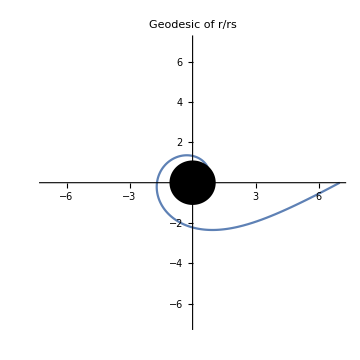

```mathematica
BHplot=ParametricPlot[{ Cos[u], Sin[u]},{u,0,2 Pi}]/.Line[l_List]:>{{Black,Polygon[l]},{Directive[AbsoluteThickness[3],Black],Line[l]}};
orbitbh=Show[ParametricPlot[{Re[r[τ]/rs]Re[Cos[ϕ[τ]]],Re[r[τ]/rs]Re[Sin[ϕ[τ]]]}/.sol[[solnumber]],{τ,τmin,ττmax},PlotRange->rmax/rs,PlotLabel->"Geodesic of r/rs",ImageSize->Medium],BHplot]
```

## Grid of All Figures

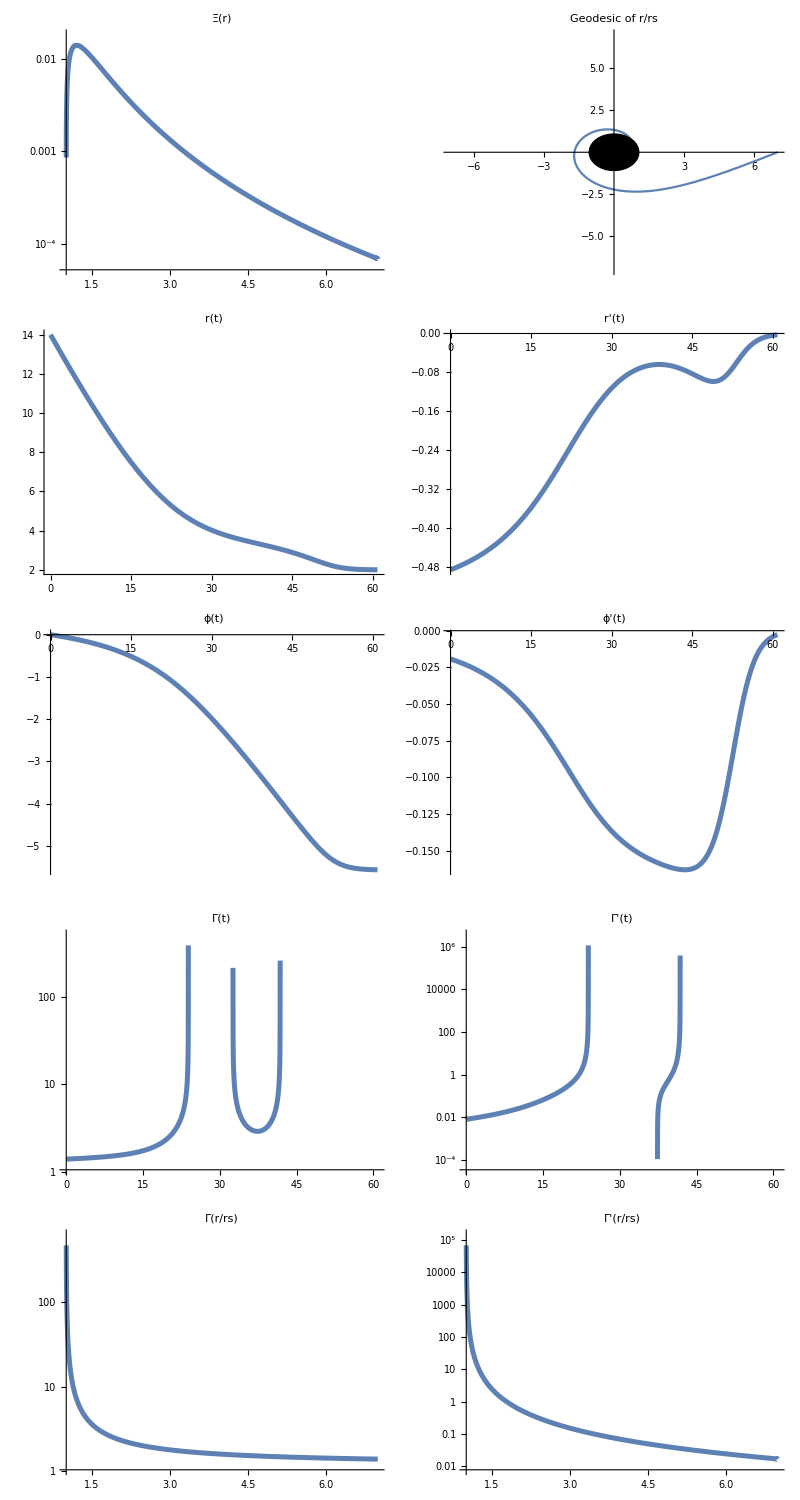

```mathematica
Grid[{
If[stoprs==True,
{vort=LogPlot[Abs[Ω[r rs]],{r,roftau[ττmax]/rs,rmax/rs},PlotLabel->"Ξ(r)",Evaluate@PlotOptions],orbitbh},
{ContourPlot[Abs[Ω[r rs]]/.t->tt,{r,roftau[ττmax]/rs,rmax/rs},{tt,toftau[τmin],toftau[ττmax]},PlotLabel->"Ω(r/rs)",Evaluate@PlotOptions],ParametricPlot3D[{Re[r[τ]/rs]Re[Cos[ϕ[τ]]]Re[Cos[θ[τ]]],Re[r[τ]/rs]Re[Sin[ϕ[τ]]]Re[Cos[θ[τ]]],Re[r[τ]/rs]Re[Sin[θ[τ]]]}/.sol[[solnumber]],{τ,τmin,ττmax},PlotLabel->"Geodesic of r/rs",Evaluate@PlotOptions]}],
{Plot[roft[t],{t,tmin,tmax},PlotLabel->"r(t)",Evaluate@PlotOptions],
roftd=Plot[roft'[t],{t,tmin,tmax},PlotLabel->"r'(t)",Evaluate@PlotOptions]},
{Plot[ϕoft[t],{t,tmin,tmax},PlotLabel->"ϕ(t)",Evaluate@PlotOptions],
ϕoftd=Plot[ϕoft'[t],{t,tmin,tmax},PlotLabel->"ϕ'(t)",Evaluate@PlotOptions]},
{Γoft1=LogPlot[Γoft[t],{t,tmin,tmax},PlotLabel->"Γ(t)",Evaluate@PlotOptions],
Γoft1d=LogPlot[Γoft'[t],{t,tmin,tmax},PlotLabel->"Γ'(t)",Evaluate@PlotOptions]},
{Γofr12=LogPlot[Abs[Γofr1[r rs]],{r,roftau[ττmax]/rs,rmax/rs},PlotLabel->"Γ(r/rs)",Evaluate@PlotOptions],
Γofr12d=LogPlot[Abs[Γofr1'[r rs]],{r,roftau[ττmax]/rs,rmax/rs},PlotLabel->"Γ'(r/rs)",Evaluate@PlotOptions]}
},Frame->All]
```

## Movie

Takes a long time, commented by default

```mathematica
(*geo1=Table[Show[ParametricPlot[{Re[r[τ]/rs]Re[Cos[ϕ[τ]]],Re[r[τ]/rs]Re[Sin[ϕ[τ]]]}/.sol[[solnumber]],{τ,τmin,ttt},PlotRange->rmax,PlotLabel->Style["Geodesic of r/rs",FontFamily->"Adobe Caslon Pro",FontSize->40],LabelStyle->Directive[FontFamily->"Adobe Caslon Pro",FontSize->35],Frame->True,FrameLabel->{"x/r_s","y/r_s"},ImageSize->1000,PlotStyle->Directive[RGBColor[0.18,0.42,0.87],Thickness[0.005]]],BHplot],{ttt,0.1,ττmax,0.05}];
Export["images/geo1_rs"<>ToString[rs]<>".swf",geo1,"FrameRate"->35];*)
```

## Publication Ready Plots

```mathematica
roftds=Show[roftd,PlotLabel->Style["",FontFamily->"Adobe Caslon Pro",FontSize->80],LabelStyle->Directive[FontFamily->"Adobe Caslon Pro",FontSize->60],FrameLabel->{"t/t_s","v^r(t)/c"},ImageSize->1000,Frame->True,FrameStyle->Thick];
ϕoftds=Show[ϕoftd,PlotLabel->Style["",FontFamily->"Adobe Caslon Pro",FontSize->80],LabelStyle->Directive[FontFamily->"Adobe Caslon Pro",FontSize->60],FrameLabel->{"t/t_s","v^ϕ(t)/c"},ImageSize->1000,Frame->True,FrameStyle->Thick];
Γoft1s=Show[Γoft1,PlotLabel->Style["",FontFamily->"Adobe Caslon Pro",FontSize->80],LabelStyle->Directive[FontFamily->"Adobe Caslon Pro",FontSize->60],FrameLabel->{"t/t_s","Γ(t)"},ImageSize->1000,Frame->True,FrameStyle->Thick];
Γoft1ds=Show[Γoft1d,PlotLabel->Style["",FontFamily->"Adobe Caslon Pro",FontSize->80],LabelStyle->Directive[FontFamily->"Adobe Caslon Pro",FontSize->60],FrameLabel->{"t/t_s","Γ'(t)"},ImageSize->1000,Frame->True,FrameStyle->Thick];
Γofr12s=Show[Γofr12,PlotLabel->Style["",FontFamily->"Adobe Caslon Pro",FontSize->80],LabelStyle->Directive[FontFamily->"Adobe Caslon Pro",FontSize->60],FrameLabel->{"r/r_s","Γ(r)"},ImageSize->1000,Frame->True,FrameStyle->Thick];
Γofr12ds=Show[Γofr12d,PlotLabel->Style["",FontFamily->"Adobe Caslon Pro",FontSize->80],LabelStyle->Directive[FontFamily->"Adobe Caslon Pro",FontSize->60],FrameLabel->{"r/r_s","Γ'(r)"},ImageSize->1000,Frame->True,FrameStyle->Thick];
vorts=Show[vort,PlotLabel->Style["",FontFamily->"Adobe Caslon Pro",FontSize->80],LabelStyle->Directive[FontFamily->"Adobe Caslon Pro",FontSize->60],FrameLabel->{"r/r_s","|Ω| a.u."},ImageSize->1000,Frame->True,FrameStyle->Thick];
```

## Save Data

## File Saving Path/Extension

```mathematica
SetDirectory[NotebookDirectory[]];
imagepath="images/";
resultspath="results/";
filextension="dat";
```

## Save Plots

```mathematica
Export[imagepath<>"roftd_rs"<>ToString[rs]<>".pdf",roftds];
Export[imagepath<>"phioftd_rs"<>ToString[rs]<>".pdf",ϕoftds];
Export[imagepath<>"gammaoft_rs"<>ToString[rs]<>".pdf",Γoft1s];
Export[imagepath<>"gammaoftd_rs"<>ToString[rs]<>".pdf",Γoft1ds];
Export[imagepath<>"gammaofr_rs"<>ToString[rs]<>".pdf",Γofr12s];
Export[imagepath<>"gammaofrd_rs"<>ToString[rs]<>".pdf",Γofr12ds];
Export[imagepath<>"vort_rs"<>ToString[rs]<>".pdf",vorts];
```

## Save Physical Quantities

```mathematica
toftau>>resultspath<>"toftau."<>filextension
roftau>>resultspath<>"roftau."<>filextension
roft>>resultspath<>"roft."<>filextension
θoft>>resultspath<>"θoft."<>filextension
ϕoft>>resultspath<>"ϕoft."<>filextension
velocityvector[t]>>resultspath<>"velocityvector."<>filextension
metricoft[t]>>resultspath<>"metricoft."<>filextension
Γoft[t]>>resultspath<>"Γoft."<>filextension
Γofr1[r]>>resultspath<>"Γofr."<>filextension
Ω[r]>>resultspath<>"vorticity."<>filextension
```